# -Graphics-

```mathematica
(4*V)/π*Sum[1/(2p+1)*Sin[(2p+1)*2π*f*t],{p,0,4}]
f=200;(* en Hz *)
V=5; (* On considère*)
```

(4 V (Sin[2 f π t]+1/3 Sin[6 f π t]+1/5 Sin[10 f π t]+1/7 Sin[14 f π t]+1/9 Sin[18 f π t]))/π

```mathematica
(20 (Sin[400 π t]+1/3 Sin[1200 π t]+1/5 Sin[2000 π t]+1/7 Sin[2800 π t]+1/9 Sin[3600 π t]))/π//Expand
```

(20 Sin[400 π t])/π+(20 Sin[1200 π t])/(3 π)+(4 Sin[2000 π t])/π+(20 Sin[2800 π t])/(7 π)+(20 Sin[3600 π t])/(9 π)

```mathematica
(20 Sin[400 π t])/π+(20 Sin[1200 π t])/(3 π)+(4 Sin[2000 π t])/π+(20 Sin[2800 π t])/(7 π)+(20 Sin[3600 π t])/(9 π)/.t->t/8000
```

(20 Sin[(π t)/20])/π+(20 Sin[(3 π t)/20])/(3 π)+(4 Sin[(π t)/4])/π+(20 Sin[(7 π t)/20])/(7 π)+(20 Sin[(9 π t)/20])/(9 π)

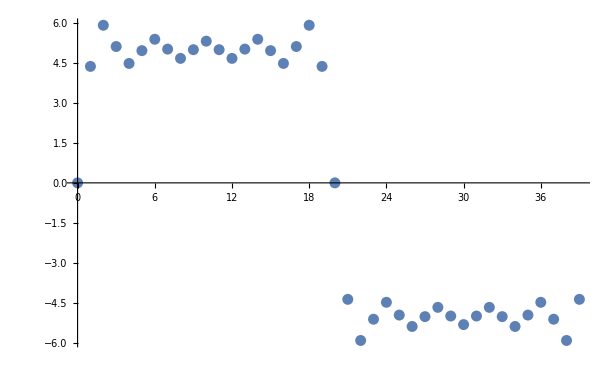

```mathematica
data=Table[{t,(20 Sin[(π t)/20])/π+(20 Sin[(3 π t)/20])/(3 π)+(4 Sin[(π t)/4])/π+(20 Sin[(7 π t)/20])/(7 π)+(20 Sin[(9 π t)/20])/(9 π)},{t,0,39,1}];
N[data//MatrixForm,32];
dataPlot=ListPlot[data]
```

```mathematica
a=(20 Sin[(π t)/20])/π+(20 Sin[(3 π t)/20])/(3 π)+(4 Sin[(π t)/4])/π+(20 Sin[(7 π t)/20])/(7 π)+(20 Sin[(9 π t)/20])/(9 π)
```

(20 Sin[(π t)/20])/π+(20 Sin[(3 π t)/20])/(3 π)+(4 Sin[(π t)/4])/π+(20 Sin[(7 π t)/20])/(7 π)+(20 Sin[(9 π t)/20])/(9 π)

```mathematica
4/π(5 Sin[(π t)/20]+5/3 Sin[(3 π t)/20]+Sin[(π t)/4]+5/7 Sin[(7 π t)/20]+5/9 Sin[(9 π t)/20])//Expand
```

(20 Sin[(π t)/20])/π+(20 Sin[(3 π t)/20])/(3 π)+(4 Sin[(π t)/4])/π+(20 Sin[(7 π t)/20])/(7 π)+(20 Sin[(9 π t)/20])/(9 π)

```mathematica
(20 Sin[(π t)/20])/π+(20 Sin[(3 π t)/20])/(3 π)+(4 Sin[(π t)/4])/π+(20 Sin[(7 π t)/20])/(7 π)+(20 Sin[(9 π t)/20])/(9 π)-a
```

0

```mathematica
(4*V)/π*Sum[1/(2p+1)*Sin[(2p+1)*ω*t],{p,0,4}]//Expand
```

(20 Sin[t ω])/π+(20 Sin[3 t ω])/(3 π)+(4 Sin[5 t ω])/π+(20 Sin[7 t ω])/(7 π)+(20 Sin[9 t ω])/(9 π)